```mathematica
SetDirectory[NotebookDirectory[]];
plotrange = {0,1300000};
VMPlot[vm_] := ListLinePlot[vmᵀ[[{3,5,7}]],PlotRange->plotrange]
```

# the dacapo test report

## test case

#### 1-2 ;mono;50M~400M ---dirty

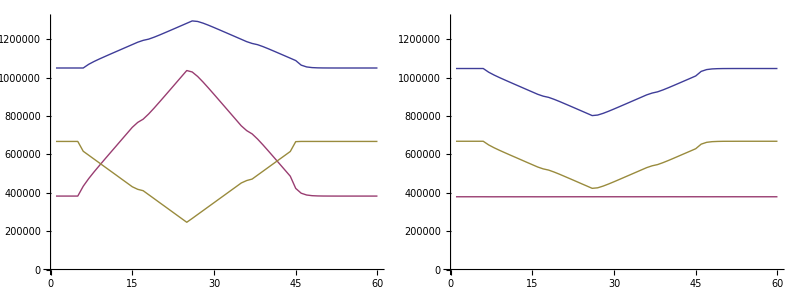

```mathematica
vm6 = Import["../dataset/1-2_mono_50M~400M/8.log"][[4;;]];
vm7 = Import["../dataset/1-2_mono_50M~400M/9.log"][[4;;]];
{{VMPlot[vm6],VMPlot[vm7]}}//TableForm
```

#### 1-4;mono;5VM;50M~400M

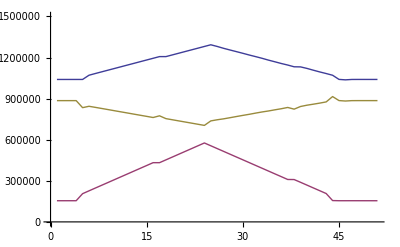
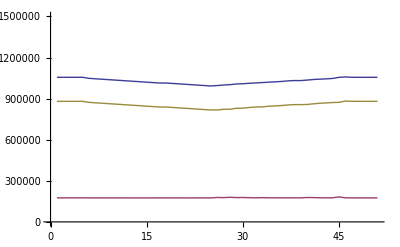
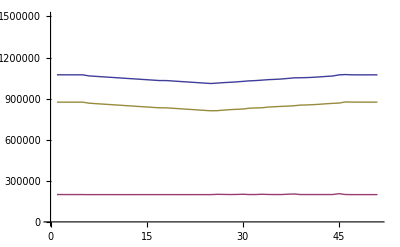
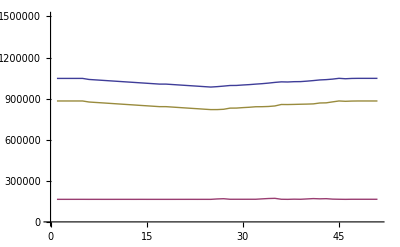
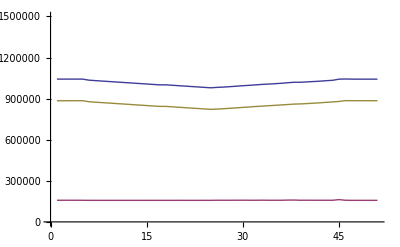
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
vm1 = Import["../dataset/1-4_mono_5VM/8.log"][[4;;]];
vm2 = Import["../dataset/1-4_mono_5VM/9.log"][[4;;]];
vm3 = Import["../dataset/1-4_mono_5VM/10.log"][[4;;]];
vm4 = Import["../dataset/1-4_mono_5VM/11.log"][[4;;]];
vm5 = Import["../dataset/1-4_mono_5VM/12.log"][[4;;]];
plotrange = {0,1500000};
{{VMPlot[vm1],VMPlot[vm2]},{VMPlot[vm3],VMPlot[vm4]},{VMPlot[vm5]}}//TableForm
```

#### 1-8;dacapo;test

```mathematica
dacapo=Import["../dataset/1_8_dacapo/dacapo.csv"][[4;;All]];
```

low load ;on is with adjust ; off is without adjust

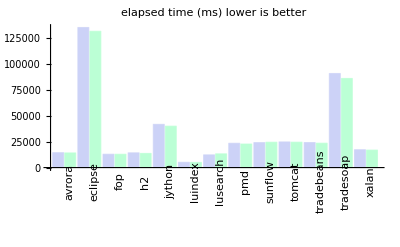
-Graphics--Graphics- | Off
-Graphics- | on

```mathematica
BarChart[dacapo[[All,2;;3]],
ChartLabels->{Placed[dacapo[[All,1]],Axis,Rotate[#,Pi/2]&],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

eat 400M;

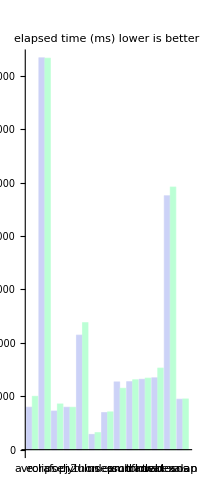
-Graphics--Graphics- | Off
-Graphics- | on

```mathematica
BarChart[dacapo[[All,4;;5]],
ChartLabels->{dacapo[[All,1]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

eat 800M;no adjust first

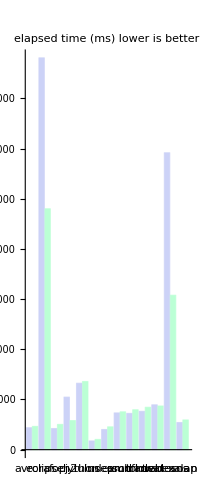
-Graphics--Graphics- | Off
-Graphics- | on

```mathematica
BarChart[dacapo[[All,6;;7]],
ChartLabels->{dacapo[[All,1]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

eat 800M again;adjust first

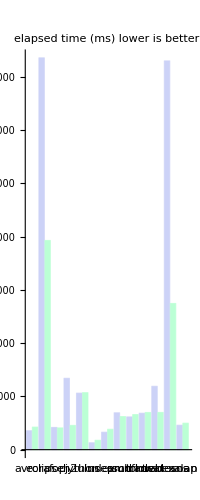
-Graphics--Graphics- | Off
-Graphics- | on

```mathematica
BarChart[dacapo[[All,8;;9]],
ChartLabels->{dacapo[[All,1]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

#### 1-9;dacapo

```mathematica
swapoff=Import["../dataset/1-9_dacapo/swap-off.log"][[3;;All,5]];
swapon=Import["../dataset/1-9_dacapo/swap-on.log"][[3;;All,5]];
dacapo = Import["../dataset/1-9_dacapo/dacapo.csv"][[2;;All]];
vm1 = Import["../dataset/1-9_dacapo/1.log"][[4;;]];
vm2 = Import["../dataset/1-9_dacapo/2.log"][[4;;]];
vm3 = Import["../dataset/1-9_dacapo/3.log"][[4;;]];
vm4 = Import["../dataset/1-9_dacapo/4.log"][[4;;]];
vm5 = Import["../dataset/1-9_dacapo/5.log"][[4;;]];
```

swap useage ,the red line is on adjust.blue line is off adjust.

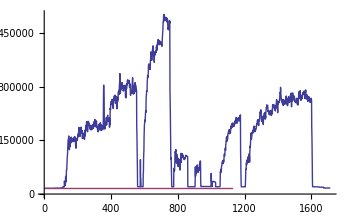

```mathematica
ListLinePlot[{swapoff,swapon}]
```

dacapo elapse time graph

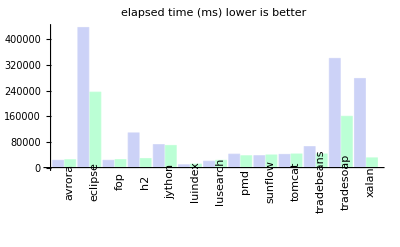
-Graphics--Graphics- | Off
-Graphics- | on

```mathematica
BarChart[dacapo[[All,2;;3]],
ChartLabels->{Placed[dacapo[[All,1]],Axis,Rotate[#,Pi/2]&],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

vm total memory change;
result:
when adjut. mmserver allocate vm1 needed memory. this part of memory is just equal memory on swap when no adjust.
allocated memory comes from other idel vms and almostly equally.

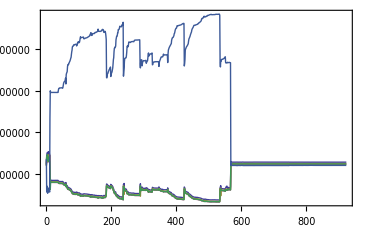

```mathematica
ListLinePlot[{vm1[[All,3]],vm2[[All,3]],vm3[[All,3]],vm4[[All,3]],vm5[[All,3]]},
Frame->True,PlotRange->All]
```